```mathematica
{n=5,y=11};
d=Table[
{d1=Table[RandomInteger[20],{y},{n-1}],
d2=Table[RandomInteger[80],{y}]},{n}];
```

```mathematica
claves={"EN","FR","GE","IT","SP"}
```

{EN,FR,GE,IT,SP}

```mathematica
d[[1]]
```

{{{7,5,6,8},{1,3,4,13},{13,5,8,5},{18,18,16,16},{10,2,9,9},{6,2,11,12},{12,20,5,19},{20,16,12,11},{20,14,0,19},{0,13,6,5},{16,11,20,20}},{59,11,57,51,59,63,51,22,4,75,47}}

```mathematica
ds={ReadList["!cut  DATOS/NW1_"<>#<>" -c 3-",Number,RecordLists->True],ReadList["!cut  DATOS/NW2_"<>#<>" -c 3-",Number,RecordLists->True]}&/@claves;
```

```mathematica
ticksx=Table[{i,10(i-1)+1900},{i,1,y,2}];
```

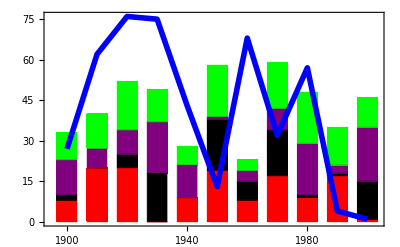

```mathematica
gDibujos[d_,l_,Colors_]:=Module[{gbc,gl},
gbc=BarChart[d[[l,1]],ChartLayout->"Stacked",ChartStyle->Delete[Colors,l],BarSpacing->.5,Axes->None];gl=ListPlot[d[[l,2]],Joined->True,PlotStyle->{Colors[[l]],Thickness[0.01]}];Show[{gbc,gl},Frame->True,FrameTicks->{ticksx,Automatic,None,None},PlotRange->All,PlotRangePadding->None]
]
Colors={Red,Blue,Black,Purple,Green};
gDibujos[d,l,Colors]
```

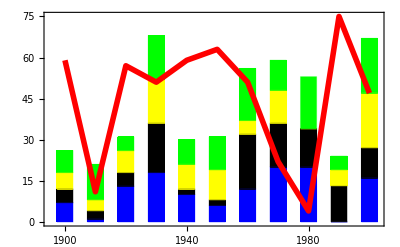
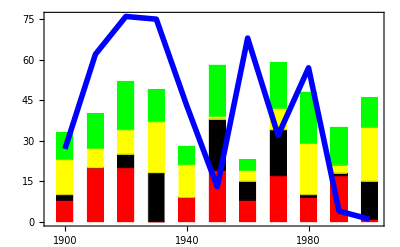
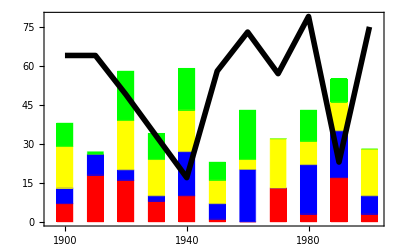
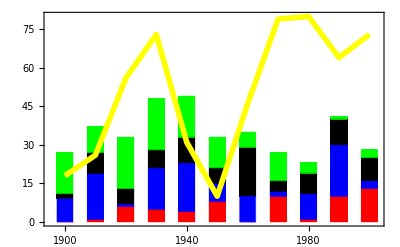
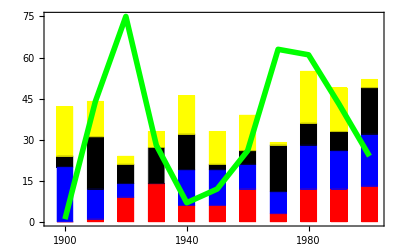

```mathematica
Table[gDibujos[d,l,Colors],{l,5}]
```